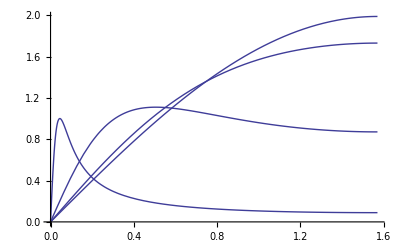

```mathematica
Plot[√(1-((β+Cos[θ])/(1+β Cos[θ]))^2)+√(1-((β-Cos[θ])/(1-β Cos[θ]))^2)/.β->{0.1,0.5,0.9,0.999},{θ,0,π/2}]
```

```mathematica
Plot3D[√(1-((β+Cos[θ])/(1+β Cos[θ]))^2)+√(1-((β-Cos[θ])/(1-β Cos[θ]))^2),{θ,0,π/2},{β,0,1}]
```

-Graphics3D-

```mathematica
Simplify[√(1-((β+Cos[θ])/(1+β Cos[θ]))^2)/.β->√(1-1/γ^2)]
```

√(Sin[θ]^2/((γ+√(1-1/γ^2) γ Cos[θ])^2))

```mathematica
Simplify[√(1-((β-Cos[θ])/(1-β Cos[θ]))^2)/.β->√(1-1/γ^2)]
```

√(Sin[θ]^2/((γ-√(1-1/γ^2) γ Cos[θ])^2))

```mathematica
Series[Sin[θ]/(γ+√(γ^2-1) Cos[θ]),{γ,-∞,2}]
```

Sin[θ]/((1+Cos[θ]) γ)+O[1/γ]^3

```mathematica
Simplify[Sin[θ]/((1+Cos[θ]) γ)+Sin[θ]/((1-Cos[θ]) γ)]
```

(2 Csc[θ])/γ

```mathematica
Simplify[Sin[θ]/(γ+√(γ^2-1) Cos[θ])+Sin[θ]/(γ+√(γ^2-1) Cos[θ])/.θ->π/2]
```

2/γ

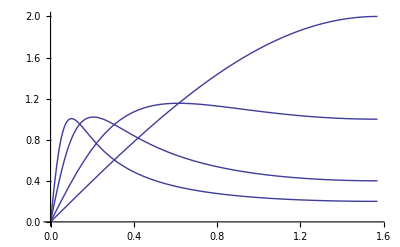

```mathematica
Plot[Sin[θ]/(γ+√(γ^2-1) Cos[θ])+Sin[θ]/(γ-√(γ^2-1) Cos[θ])/.γ->{1,2,5,10},{θ,0,π/2}]
```

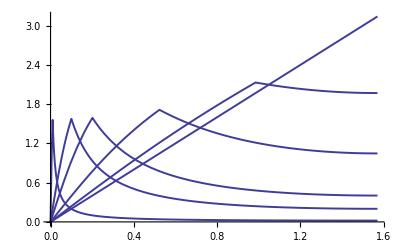

```mathematica
Plot[ArcSin[Sin[θ]/(γ+√(γ^2-1) Cos[θ])]+ArcSin[Sin[θ]/(γ-√(γ^2-1) Cos[θ])]/.γ->{1,1.2,2,5,10,100},{θ,0,π/2},PlotStyle->{Thickness[0.0035]}]
```

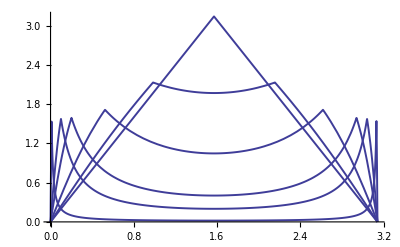

```mathematica
Plot[ArcSin[Sin[θ]/(γ+√(γ^2-1) Cos[θ])]+ArcSin[Sin[θ]/(γ-√(γ^2-1) Cos[θ])]/.γ->{1,1.2,2,5,10,100},{θ,0,π},PlotStyle->{Thickness[0.0035]}]
```

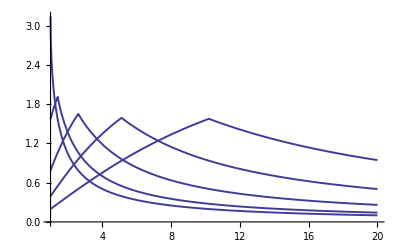

```mathematica
Plot[ArcSin[Sin[θ]/(γ+√(γ^2-1) Cos[θ])]+ArcSin[Sin[θ]/(γ-√(γ^2-1) Cos[θ])]/.θ->{π/32,π/16,π/8,π/4,π/2},{γ,1,20},PlotStyle->{Thickness[0.0035]},AxesOrigin->{1,0},PlotRange->{Full,Full}]
```

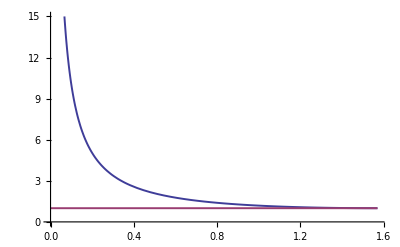

```mathematica
Plot[{1/Sin[θ],1},{θ,0,π/2},PlotStyle->{Thickness[0.0035]},PlotRange->{Full,{0,15}}]
```

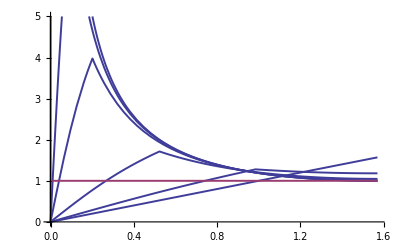

```mathematica
Plot[{γ/2(ArcSin[Sin[θ]/(γ+√(γ^2-1) Cos[θ])]+ArcSin[Sin[θ]/(γ-√(γ^2-1) Cos[θ])])/.γ->{1,1.2,2,5,10,100},1},{θ,0,π/2},PlotStyle->{Thickness[0.0035]},PlotRange->{Full,{0,5}}]
```